```mathematica
Quit[]
```

## Preliminaries

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
NotebookDirectory[];
SetDirectory[NotebookDirectory[]];
```

```mathematica
$Assumptions={Re[s]>4 m^2,m ∈ Reals};
```

```mathematica
ϵ := 10^-8;
iϵ:=I ϵ
```

```mathematica
jpacBlue=RGBColor[31/256,119/256,180/256];
jpacRed=RGBColor[214/256,39/256,40/256];
jpacGreen=RGBColor[0/256,158/256,115/256];
jpacGray = RGBColor[50/256,50/256,50/256];
jpacThick := Thickness[0.007];
```

```mathematica
sthRectangle[sL_,sR_]:={LightGray,Rectangle[{sL,-999},{sR,999}]}
sthColor[color_,sL_,sR_]:={color,Rectangle[{sL,-999},{sR,999}]}
vert[x_]:=Line[{{x,-999},{x,999}}]
frameLabel[label_]:=Style[label,Directive[jpacGray,Bold,12]]
frameLabel[label_,variable_]:=frameLabel[label<> ToString[variable]]
frameLabel[label_,variable_,units_]:=frameLabel[label<> ToString[variable]<>units]
```

```mathematica
jpacOptions:={PlotRange->{Automatic,Automatic},
Frame->True,
FrameTicksStyle->Directive[jpacGray,Bold,12],
ImageSize->Medium,
AspectRatio->1,
PlotStyle->{{jpacBlue, jpacThick},{jpacRed, jpacThick},{jpacGreen, jpacThick},{jpacGreen, jpacThick}},
FrameLabel->{{None ,None},{frameLabel["s [GeV^2]"],None}}}
```

## σ Trajectory

### Parameters and definitions

```mathematica
q[s_]=√((s-4 m^2)/4);
ρ[s_]=2 q[s]/(√s);
q2hat[s_]=q[s]^2/Λ^2;
```

```mathematica
m=0.13957000;
Λ=√2;
αth=-0.063754;
gσ=0.13668381;
gP=1.8862193;
c=0.013793376;
Imα[s_]=ρ[s]/gσ(gσ+gP(αth+c ρ[s]Log[s/(4 m^2)]))^2;
```

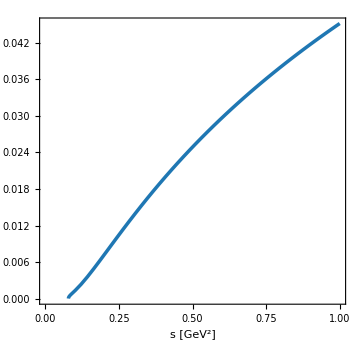

```mathematica
Plot[Imα[s],{s,0,1},Evaluate[jpacOptions]]
```

### On the first sheet

Define the dispersion integral without an iϵ prescription, remember to put it in by hand in the argument!

```mathematica
dispInt[s_]:=s/π NIntegrate[(Imα[x]-Imα[s])/(x(x-s)),{x,4 m^2,∞},Method->{Automatic,"SymbolicProcessing"->0}]-Imα[s]/π Log[1-s/(4 m^2)]
dispth = Re[dispInt[4 m^2 + I ϵ]];
αI[s_]:=αth + dispInt[s]-dispth
fI[s_]:=gσ/(-αI[s])-gP
```

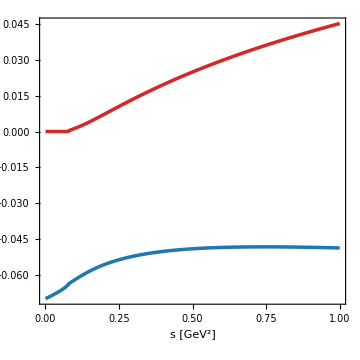

```mathematica
Plot[{αI[s+iϵ]//Re,αI[s+iϵ] //Im},{s,0,1},Evaluate[jpacOptions]]
```

Plot the resulting partial wave amplitude

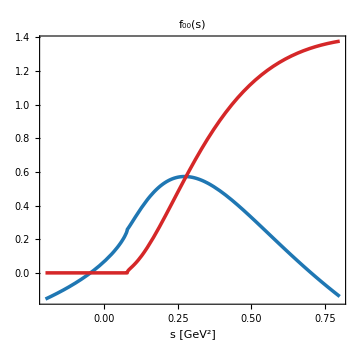

```mathematica
Plot[{fI[s+iϵ]//Re,fI[s+iϵ] //Im},{s,-0.2,0.8},Evaluate[jpacOptions],PlotLabel->frameLabel["f_00(s)"]]
```

### On the unphysical sheet

The second sheet is stitched to the first by the discontinuity

```mathematica
(* ------------------------------------------------- *)
αII[s_]:=αI[s-iϵ] +2I Imα[s]
fII[s_]:=gσ/(-αII[s])-gP
(* ------------------------------------------------- *)
```

```mathematica
PoleSearch[f_,xran_,yran_]:= NMinimize[{Abs[f[x+I y]]^-1, x>xran[[1]]&& x<xran[[2]]&& y>yran[[1]]&& y<yran[[2]]},{x,y},AccuracyGoal->10,PrecisionGoal->10,MaxIterations->50,Method->"SimulatedAnnealing"]
```

```mathematica
ResParams[f_,sp_?NumericQ]:=
Module[{gi,g},
Print["√s_p = (", √sp*10^3, ") MeV"];
Print["M = ", Re[√sp]*10^3, " MeV"];
Print["Γ = ", -2Im[√sp]*10^3, " MeV"];
gi={};
AppendTo[gi,√Quiet@NLimit[-16π f[s](s-sp),s->sp,WorkingPrecision->50, Direction->1,Method->"SequenceLimit"]];
AppendTo[gi,√Quiet@NLimit[-16π f[s](s-sp),s->sp,WorkingPrecision->50,Direction->-1,Method->"SequenceLimit"]];
AppendTo[gi,√Quiet@NLimit[-16π f[s](s-sp),s->sp,WorkingPrecision->50, Direction->-I,Method->"SequenceLimit"]];
AppendTo[gi,√Quiet@NLimit[-16π f[s](s-sp),s->sp,WorkingPrecision->50, Direction->I,Method->"SequenceLimit"]];

g=Mean[gi];
Print["g's = ", Transpose[gi]//MatrixForm];
Print["|g_avg| = ", Abs[g]];
Print["arg(g_avg) = ", Arg[g] 180/π];
]
```

#### Poles using Imα[s]

Look for poles by continuing the aII as above, i.e. adding 2 I Imα naively

```mathematica
Plot3D[Abs[fII[x+I y]],{x,+ϵ,0.1},{y,-0.7,-ϵ},AxesLabel->{frameLabel["Re s"], frameLabel["Im s"]},PlotRange->{0,30},ImageSize->Large]
```

-Graphics3D-

```mathematica
pole=Quiet@PoleSearch[fII,{ϵ,0.5},{-0.7,-0.1}]
ResParams[fII,(x+I y)/.pole[[2]]]
```

{4.38754×10^-9,{x→0.00136038,y→-0.460093}}

√s_p = (480.341-478.923 ⅈ) MeV

M = 480.341 MeV

Γ = 957.847 MeV

g's = (2.0788-7.52428 ⅈ
2.07923-7.52455 ⅈ
2.07889-7.52463 ⅈ
2.07915-7.5242 ⅈ)

|g_avg| = 7.80635

arg(g_avg) = -74.5544

```mathematica
(* Plot what it looks like stitched to the first sheet *)
```

```mathematica
α[s_]:=If[Im[s]>=0,αI[s],αII[s]]
Plot3D[Abs[gσ/(-α[x+I y])-gP],{x,0,0.5},{y,-0.9,0.5},AxesLabel->{frameLabel["Re s"], frameLabel["Im s"]},ImageSize->Large,PlotRange->{0,15}]
```

-Graphics3D-

#### Continued Fractions definitions

```mathematica
generateCoeffs[svals_,f_]:=Module[{N,i,current,next, last, as,fvals},
(* Set up vector of f(s) *)
N=Length[svals];
fvals=f[svals];
(* empty list to output resulting coeffs *)
as={};
(* first coefficient *)
AppendTo[as,1./(svals[[2]]-svals[[1]])(fvals[[1]]/fvals[[2]]-1)];
(* loop over i = 2 to N-1 coefficients *)
Do[
last = 0; current = 0;
last= (as[[1]](svals[[l+1]]-svals[[1]]))/(1.-fvals[[1]]/fvals[[l+1]]);
current = last;
Do[
current = (as[[j]](svals[[l+1]]-svals[[j]]))/(1.+last);
last = current;
,{j,2,l-1}];
AppendTo[as, (1+current)/(svals[[l]]-svals[[l+1]])];
,{l,2,N-1}];
(* return list *)
as
]
generateCF[N_,srange_,f_,s_]:=
Module[{svals,as,fraction,current},
svals=Range[srange[[1]],srange[[2]],(srange[[2]]-srange[[1]])/N];
as = generateCoeffs[svals,f];
fraction =  as[[N]]*(s-svals[[N]]);
Do[
current = (as[[N-j]](s-svals[[N-j]]))/(1+fraction);
fraction = current;
,{j,1,N-1}];
f[svals[[1]]]/(1+fraction)
]
ContFrac[N_,srange_,f_]:=generateCF[N,srange,f,s];
```

#### Poles with CFs

```mathematica
(* Start with N = 50 *)
```

```mathematica
fCF[s_]=ContFrac[50,{4 m^2,1.0},fII];
Plot3D[Abs[fCF[x+I y]],{x,+ϵ,0.1},{y,-0.7,-ϵ},AxesLabel->{frameLabel["Re s"], frameLabel["Im s"]},PlotRange->{0,30},ImageSize->Large]
pole=PoleSearch[fCF,{0.0,0.5},{-0.7,-0.0}]
ResParams[fCF,(x+I y)/.pole[[2]]]
```

-Graphics3D-

{8.45435×10^-9,{x→0.0304708,y→-0.467231}}

√s_p = (499.347-467.842 ⅈ) MeV

M = 499.347 MeV

Γ = 935.684 MeV

g's = (2.40651-7.52579 ⅈ
2.40741-7.52628 ⅈ
2.40671-7.52647 ⅈ
2.40719-7.52559 ⅈ)

|g_avg| = 7.90156

arg(g_avg) = -72.2648

```mathematica
(* Increase to N = 500 *)
```

```mathematica
fCF[s_]=ContFrac[500,{4 m^2,1.0},fII];
Plot3D[Abs[fCF[x+I y]],{x,+ϵ,0.1},{y,-0.7,-ϵ},AxesLabel->{frameLabel["Re s"], frameLabel["Im s"]},PlotRange->{0,30},ImageSize->Large]
pole=PoleSearch[fCF,{0.0,0.5},{-0.7,-0.0}]
ResParams[fCF,(x+I y)/.pole[[2]]]
```

-Graphics3D-

{2.29861×10^-11,{x→0.00263779,y→-0.459336}}

√s_p = (480.615-477.863 ⅈ) MeV

M = 480.615 MeV

Γ = 955.726 MeV

g's = (2.09282-7.51961 ⅈ
2.09282-7.5196 ⅈ
2.09283-7.5196 ⅈ
2.09282-7.51961 ⅈ)

|g_avg| = 7.80541

arg(g_avg) = -74.4473

#### Poles with Pade

```mathematica
(* start with one value of s0 *)
```

```mathematica
s0=0.9;
nPade =10;
PadeApproximant[Imα[x],{x,s0,nPade}];
ImαPade[x_]=%;
αPade[x_]:=αI[x-iϵ]+ 2 I  ImαPade[x];
fPade[x_]:=gσ/(-αPade[x-iϵ])-gP;
Plot3D[Abs[fPade[x+I y]],{x,+ϵ,0.1},{y,-0.7,-ϵ},AxesLabel->{frameLabel["Re s"], frameLabel["Im s"]},PlotRange->{0,30},ImageSize->Large]
pole=Quiet@PoleSearch[fPade,{ϵ,0.5},{-0.7,-ϵ}]
ResParams[fPade,(x+I y)/.pole[[2]]]
```

-Graphics3D-

{6.90272×10^-9,{x→0.0013603,y→-0.460093}}

√s_p = (480.341-478.923 ⅈ) MeV

M = 480.341 MeV

Γ = 957.846 MeV

g's = (2.07857-7.52438 ⅈ
2.07936-7.52453 ⅈ
2.0789-7.52483 ⅈ
2.07904-7.52407 ⅈ)

|g_avg| = 7.80638

arg(g_avg) = -74.5548

```mathematica
(* vary s0 *)
```

```mathematica
s0=1.2;
nPade =10;
PadeApproximant[Imα[x],{x,s0,nPade}];
ImαPade[x_]=%;
αPade[x_]:=αI[x-iϵ]+ 2 I  ImαPade[x];
fPade[x_]:=gσ/(-αPade[x-iϵ])-gP;
Plot3D[Abs[fPade[x+I y]],{x,+ϵ,0.1},{y,-0.7,-ϵ},AxesLabel->{frameLabel["Re s"], frameLabel["Im s"]},PlotRange->{0,30},ImageSize->Large]
pole=Quiet@PoleSearch[fPade,{ϵ,0.5},{-0.7,-ϵ}]
ResParams[fPade,(x+I y)/.pole[[2]]]
```

-Graphics3D-

{6.58689×10^-9,{x→0.00135961,y→-0.460094}}

√s_p = (480.342-478.924 ⅈ) MeV

M = 480.342 MeV

Γ = 957.848 MeV

g's = (2.07874-7.52447 ⅈ
2.07951-7.52437 ⅈ
2.07918-7.52478 ⅈ
2.07908-7.52405 ⅈ)

|g_avg| = 7.80638

arg(g_avg) = -74.5536

```mathematica
(* Vary N *)
```

```mathematica
s0=0.8;
nPade =20;
PadeApproximant[Imα[x],{x,s0,nPade}];
ImαPade[x_]=%;
αPade[x_]:=αI[x-iϵ]+ 2 I  ImαPade[x];
fPade[x_]:=gσ/(-αPade[x-iϵ])-gP;
Plot3D[Abs[fPade[x+I y]],{x,+ϵ,0.1},{y,-0.7,-ϵ},AxesLabel->{frameLabel["Re s"], frameLabel["Im s"]},PlotRange->{0,30},ImageSize->Large]
pole=Quiet@PoleSearch[fPade,{ϵ,0.5},{-0.7,-ϵ}]
ResParams[fPade,(x+I y)/.pole[[2]]]
```

-Graphics3D-

{6.83332×10^-9,{x→0.00136038,y→-0.460093}}

√s_p = (480.341-478.923 ⅈ) MeV

M = 480.341 MeV

Γ = 957.847 MeV

g's = (2.07861-7.52443 ⅈ
2.07941-7.52441 ⅈ
2.07903-7.52479 ⅈ
2.07901-7.52403 ⅈ)

|g_avg| = 7.80635

arg(g_avg) = -74.5544

### Excited σ?

```mathematica
fpII[s_]:=αII[s]
fpCF[s_]=ContFrac[40,{4 m^2,1.0},fpII];
Plot3D[Re[fpCF[x+I y]],{x,+ϵ,100},{y,-100,-ϵ},AxesLabel->{frameLabel["Re s"], frameLabel["Im s"],frameLabel["-α_σ"]},ImageSize->Large]
```

-Graphics3D-